```mathematica
Lo[S_,K_,r_,T_]:=Log[S/K] + r*T
```

```mathematica
Z[σ_,T_]:=(σ*√T)/(√2)
```

```mathematica
BSSeriesNM[S_,K_,r_,σ_,T_,n_,m_]:=K*ⅇ^(-r*T)/2 * (-1)^n/(n! Gamma[1+(m-n)/2])*(Z[σ,T]^2 -Lo[S,K,r,T])^n*Z[σ,T]^(m-n)
```

```mathematica
Table[BSSeriesNM[100,100,0.05,0.2,1,n,m],{n,0,10},{m,1,10}]//MatrixForm
```

(7.58971 | 0.951229 | 0.101196 | 0.00951229 | 0.000809569 | 0.0000634153 | 4.62611×10^-6 | 3.17076×10^-7 | 2.05605×10^-8 | 1.26831×10^-9
1.42684 | 0.227691 | 0.0285369 | 0.00303589 | 0.000285369 | 0.0000242871 | 1.90246×10^-6 | 1.38783×10^-7 | 9.51229×10^-9 | 6.16815×10^-10
0.0853843 | 0.0214027 | 0.00341537 | 0.000428053 | 0.0000455383 | 4.28053×10^-6 | 3.64306×10^-7 | 2.85369×10^-8 | 2.08175×10^-9 | 1.42684×10^-10
0. | 0.000853843 | 0.000214027 | 0.0000341537 | 4.28053×10^-6 | 4.55383×10^-7 | 4.28053×10^-8 | 3.64306×10^-9 | 2.85369×10^-10 | 2.08175×10^-11
-0.000160096 | 0. | 6.40382×10^-6 | 1.6052×10^-6 | 2.56153×10^-7 | 3.2104×10^-8 | 3.41537×10^-9 | 3.2104×10^-10 | 2.7323×10^-11 | 2.14027×10^-12
0. | -9.60573×10^-7 | 0. | 3.84229×10^-8 | 9.6312×10^-9 | 1.53692×10^-9 | 1.92624×10^-10 | 2.04922×10^-11 | 1.92624×10^-12 | 1.63938×10^-13
3.60215×10^-7 | 0. | -4.80287×10^-9 | 0. | 1.92115×10^-10 | 4.8156×10^-11 | 7.68458×10^-12 | 9.6312×10^-13 | 1.02461×10^-13 | 9.6312×10^-15
0. | 1.54378×10^-9 | 0. | -2.05837×10^-11 | 0. | 8.23348×10^-13 | 2.06383×10^-13 | 3.29339×10^-14 | 4.12766×10^-15 | 4.39119×10^-16
-7.23646×10^-10 | 0. | 5.78917×10^-12 | 0. | -7.71889×10^-14 | 0. | 3.08756×10^-15 | 7.73936×10^-16 | 1.23502×10^-16 | 1.54787×10^-17
0. | -2.41215×10^-12 | 0. | 1.92972×10^-14 | 0. | -2.57296×10^-16 | 0. | 1.02919×10^-17 | 2.57979×10^-18 | 4.11674×10^-19
1.26638×10^-12 | 0. | -7.23646×10^-15 | 0. | 5.78917×10^-17 | 0. | -7.71889×10^-19 | 0. | 3.08756×10^-20 | 7.73936×10^-21)

```mathematica
BSSeries[S_,K_,r_,σ_,T_]:=K*ⅇ^(-r*T)/2 *Sum[Sum[ (-1)^n/(n! Gamma[1+(m-n)/2])*(Z[σ,T]^2 -Lo[S,K,r,T])^n*Z[σ,T]^(m-n),{m,1,10}],{n,0,10}]
```

```mathematica
Expand[BSSeries[S,K,r,σ,T],σ Sqrt[T]]
```

1/2 ⅇ^(-r T) K (r T+√(2/π) √T σ+1/3 √(2/π) T^(3/2) σ^3+(T^2 σ^4)/8+1/15 √(2/π) T^(5/2) σ^5+(T^3 σ^6)/48+1/105 √(2/π) T^(7/2) σ^7+(T^4 σ^8)/384+1/945 √(2/π) T^(9/2) σ^9+(T^5 σ^10)/3840-√(2/π) √T σ (-r T+(T σ^2)/2-Log[S/K])-1/2 T σ^2 (-r T+(T σ^2)/2-Log[S/K])-1/3 √(2/π) T^(3/2) σ^3 (-r T+(T σ^2)/2-Log[S/K])-1/8 T^2 σ^4 (-r T+(T σ^2)/2-Log[S/K])-1/15 √(2/π) T^(5/2) σ^5 (-r T+(T σ^2)/2-Log[S/K])-1/48 T^3 σ^6 (-r T+(T σ^2)/2-Log[S/K])-1/105 √(2/π) T^(7/2) σ^7 (-r T+(T σ^2)/2-Log[S/K])-1/384 T^4 σ^8 (-r T+(T σ^2)/2-Log[S/K])-1/945 √(2/π) T^(9/2) σ^9 (-r T+(T σ^2)/2-Log[S/K])+1/2 (-r T+(T σ^2)/2-Log[S/K])^2+((-r T+(T σ^2)/2-Log[S/K])^2)/(√(2 π) √T σ)+(√T σ (-r T+(T σ^2)/2-Log[S/K])^2)/(√(2 π))+1/4 T σ^2 (-r T+(T σ^2)/2-Log[S/K])^2+(T^(3/2) σ^3 (-r T+(T σ^2)/2-Log[S/K])^2)/(3 √(2 π))+1/16 T^2 σ^4 (-r T+(T σ^2)/2-Log[S/K])^2+(T^(5/2) σ^5 (-r T+(T σ^2)/2-Log[S/K])^2)/(15 √(2 π))+1/96 T^3 σ^6 (-r T+(T σ^2)/2-Log[S/K])^2+(T^(7/2) σ^7 (-r T+(T σ^2)/2-Log[S/K])^2)/(105 √(2 π))+1/768 T^4 σ^8 (-r T+(T σ^2)/2-Log[S/K])^2-1/6 (-r T+(T σ^2)/2-Log[S/K])^3-((-r T+(T σ^2)/2-Log[S/K])^3)/(3 √(2 π) √T σ)-(√T σ (-r T+(T σ^2)/2-Log[S/K])^3)/(3 √(2 π))-1/12 T σ^2 (-r T+(T σ^2)/2-Log[S/K])^3-(T^(3/2) σ^3 (-r T+(T σ^2)/2-Log[S/K])^3)/(9 √(2 π))-1/48 T^2 σ^4 (-r T+(T σ^2)/2-Log[S/K])^3-(T^(5/2) σ^5 (-r T+(T σ^2)/2-Log[S/K])^3)/(45 √(2 π))-1/288 T^3 σ^6 (-r T+(T σ^2)/2-Log[S/K])^3-(T^(7/2) σ^7 (-r T+(T σ^2)/2-Log[S/K])^3)/(315 √(2 π))+1/24 (-r T+(T σ^2)/2-Log[S/K])^4-((-r T+(T σ^2)/2-Log[S/K])^4)/(12 √(2 π) T^(3/2) σ^3)+((-r T+(T σ^2)/2-Log[S/K])^4)/(12 √(2 π) √T σ)+(√T σ (-r T+(T σ^2)/2-Log[S/K])^4)/(12 √(2 π))+1/48 T σ^2 (-r T+(T σ^2)/2-Log[S/K])^4+(T^(3/2) σ^3 (-r T+(T σ^2)/2-Log[S/K])^4)/(36 √(2 π))+1/192 T^2 σ^4 (-r T+(T σ^2)/2-Log[S/K])^4+(T^(5/2) σ^5 (-r T+(T σ^2)/2-Log[S/K])^4)/(180 √(2 π))+(T^3 σ^6 (-r T+(T σ^2)/2-Log[S/K])^4)/1152-1/120 (-r T+(T σ^2)/2-Log[S/K])^5+((-r T+(T σ^2)/2-Log[S/K])^5)/(60 √(2 π) T^(3/2) σ^3)-((-r T+(T σ^2)/2-Log[S/K])^5)/(60 √(2 π) √T σ)-(√T σ (-r T+(T σ^2)/2-Log[S/K])^5)/(60 √(2 π))-1/240 T σ^2 (-r T+(T σ^2)/2-Log[S/K])^5-(T^(3/2) σ^3 (-r T+(T σ^2)/2-Log[S/K])^5)/(180 √(2 π))-1/960 T^2 σ^4 (-r T+(T σ^2)/2-Log[S/K])^5-(T^(5/2) σ^5 (-r T+(T σ^2)/2-Log[S/K])^5)/(900 √(2 π))+1/720 (-r T+(T σ^2)/2-Log[S/K])^6+((-r T+(T σ^2)/2-Log[S/K])^6)/(120 √(2 π) T^(5/2) σ^5)-((-r T+(T σ^2)/2-Log[S/K])^6)/(360 √(2 π) T^(3/2) σ^3)+((-r T+(T σ^2)/2-Log[S/K])^6)/(360 √(2 π) √T σ)+(√T σ (-r T+(T σ^2)/2-Log[S/K])^6)/(360 √(2 π))+(T σ^2 (-r T+(T σ^2)/2-Log[S/K])^6)/1440+(T^(3/2) σ^3 (-r T+(T σ^2)/2-Log[S/K])^6)/(1080 √(2 π))+(T^2 σ^4 (-r T+(T σ^2)/2-Log[S/K])^6)/5760-((-r T+(T σ^2)/2-Log[S/K])^7)/5040-((-r T+(T σ^2)/2-Log[S/K])^7)/(840 √(2 π) T^(5/2) σ^5)+((-r T+(T σ^2)/2-Log[S/K])^7)/(2520 √(2 π) T^(3/2) σ^3)-((-r T+(T σ^2)/2-Log[S/K])^7)/(2520 √(2 π) √T σ)-(√T σ (-r T+(T σ^2)/2-Log[S/K])^7)/(2520 √(2 π))-(T σ^2 (-r T+(T σ^2)/2-Log[S/K])^7)/10080-(T^(3/2) σ^3 (-r T+(T σ^2)/2-Log[S/K])^7)/(7560 √(2 π))+((-r T+(T σ^2)/2-Log[S/K])^8)/40320-((-r T+(T σ^2)/2-Log[S/K])^8)/(1344 √(2 π) T^(7/2) σ^7)+((-r T+(T σ^2)/2-Log[S/K])^8)/(6720 √(2 π) T^(5/2) σ^5)-((-r T+(T σ^2)/2-Log[S/K])^8)/(20160 √(2 π) T^(3/2) σ^3)+((-r T+(T σ^2)/2-Log[S/K])^8)/(20160 √(2 π) √T σ)+(√T σ (-r T+(T σ^2)/2-Log[S/K])^8)/(20160 √(2 π))+(T σ^2 (-r T+(T σ^2)/2-Log[S/K])^8)/80640-((-r T+(T σ^2)/2-Log[S/K])^9)/362880+((-r T+(T σ^2)/2-Log[S/K])^9)/(12096 √(2 π) T^(7/2) σ^7)-((-r T+(T σ^2)/2-Log[S/K])^9)/(60480 √(2 π) T^(5/2) σ^5)+((-r T+(T σ^2)/2-Log[S/K])^9)/(181440 √(2 π) T^(3/2) σ^3)-((-r T+(T σ^2)/2-Log[S/K])^9)/(181440 √(2 π) √T σ)-(√T σ (-r T+(T σ^2)/2-Log[S/K])^9)/(181440 √(2 π))+((-r T+(T σ^2)/2-Log[S/K])^10)/3628800+((-r T+(T σ^2)/2-Log[S/K])^10)/(17280 √(2 π) T^(9/2) σ^9)-((-r T+(T σ^2)/2-Log[S/K])^10)/(120960 √(2 π) T^(7/2) σ^7)+((-r T+(T σ^2)/2-Log[S/K])^10)/(604800 √(2 π) T^(5/2) σ^5)-((-r T+(T σ^2)/2-Log[S/K])^10)/(1814400 √(2 π) T^(3/2) σ^3)+((-r T+(T σ^2)/2-Log[S/K])^10)/(1814400 √(2 π) √T σ)+Log[S/K])

```mathematica
CoefficientList[%,σ Sqrt[T]]//TraditionalForm
```

1/(7257600 √π T^(9/2) σ^9)ⅇ^(-r T) K (945 √π T^(19/2) σ^19+3840 √2 T^9 σ^18+3840 √2 T^9 (-(T σ^2)/2+r T+log(S/K)) σ^18+9450 √π T^(17/2) σ^17+4725 √π T^(17/2) (-(T σ^2)/2+r T+log(S/K))^2 σ^17+9450 √π T^(17/2) (-(T σ^2)/2+r T+log(S/K)) σ^17+34560 √2 T^8 σ^16+5760 √2 T^8 (-(T σ^2)/2+r T+log(S/K))^3 σ^16+4320 √2 T^8 (-T σ^2+2 r T+2 log(S/K))^2 σ^16+34560 √2 T^8 (-(T σ^2)/2+r T+log(S/K)) σ^16+75600 √π T^(15/2) σ^15+3150 √π T^(15/2) (-(T σ^2)/2+r T+log(S/K))^4 σ^15+12600 √π T^(15/2) (-(T σ^2)/2+r T+log(S/K))^3 σ^15+9450 √π T^(15/2) (-T σ^2+2 r T+2 log(S/K))^2 σ^15+75600 √π T^(15/2) (-(T σ^2)/2+r T+log(S/K)) σ^15+241920 √2 T^7 σ^14-63 √2 T^7 (T (σ^2-2 r)-2 log(S/K))^5 σ^14+630 √2 T^7 (-T σ^2+2 r T+2 log(S/K))^4 σ^14+40320 √2 T^7 (-(T σ^2)/2+r T+log(S/K))^3 σ^14+30240 √2 T^7 (-T σ^2+2 r T+2 log(S/K))^2 σ^14+241920 √2 T^7 (-(T σ^2)/2+r T+log(S/K)) σ^14+453600 √π T^(13/2) σ^13+630 √π T^(13/2) (-(T σ^2)/2+r T+log(S/K))^6 σ^13+3780 √π T^(13/2) (-(T σ^2)/2+r T+log(S/K))^5 σ^13+18900 √π T^(13/2) (-(T σ^2)/2+r T+log(S/K))^4 σ^13+75600 √π T^(13/2) (-(T σ^2)/2+r T+log(S/K))^3 σ^13+56700 √π T^(13/2) (-T σ^2+2 r T+2 log(S/K))^2 σ^13+453600 √π T^(13/2) (-(T σ^2)/2+r T+log(S/K)) σ^13+240 √2 T^6 (-(T σ^2)/2+r T+log(S/K))^7 σ^12+1209600 √2 T^6 σ^12+1680 √2 T^6 (-(T σ^2)/2+r T+log(S/K))^6 σ^12-315 √2 T^6 (T (σ^2-2 r)-2 log(S/K))^5 σ^12+3150 √2 T^6 (-T σ^2+2 r T+2 log(S/K))^4 σ^12+201600 √2 T^6 (-(T σ^2)/2+r T+log(S/K))^3 σ^12+604800 √2 T^6 (-(T σ^2)/2+r T+log(S/K))^2 σ^12+1209600 √2 T^6 (-(T σ^2)/2+r T+log(S/K)) σ^12+45 √π T^(11/2) (-(T σ^2)/2+r T+log(S/K))^8 σ^11+360 √π T^(11/2) (-(T σ^2)/2+r T+log(S/K))^7 σ^11+2520 √π T^(11/2) (-(T σ^2)/2+r T+log(S/K))^6 σ^11+15120 √π T^(11/2) (-(T σ^2)/2+r T+log(S/K))^5 σ^11+4725 √π T^(11/2) (-T σ^2+2 r T+2 log(S/K))^4 σ^11+302400 √π T^(11/2) (-(T σ^2)/2+r T+log(S/K))^3 σ^11+907200 √π T^(11/2) (-(T σ^2)/2+r T+log(S/K))^2 σ^11+1814400 √π T^(11/2) (-(T σ^2)/2+r T+log(S/K)) σ^11+10 √2 T^5 ((-(T σ^2)/2+r T+log(S/K))^9+9 (-(T σ^2)/2+r T+log(S/K))^8+72 (-(T σ^2)/2+r T+log(S/K))^7+504 (-(T σ^2)/2+r T+log(S/K))^6+3024 (-(T σ^2)/2+r T+log(S/K))^5+362880 (-(T σ^2)/2+r T+log(S/K))+945 (-T σ^2+2 r T+2 log(S/K))^4+7560 (-T σ^2+2 r T+2 log(S/K))^3+45360 (-T σ^2+2 r T+2 log(S/K))^2+362880) σ^10+√π T^(9/2) (-(T σ^2)/2+r T+log(S/K))^10 σ^9+10 √π T^(9/2) (-(T σ^2)/2+r T+log(S/K))^9 σ^9+90 √π T^(9/2) (-(T σ^2)/2+r T+log(S/K))^8 σ^9+720 √π T^(9/2) (-(T σ^2)/2+r T+log(S/K))^7 σ^9+5040 √π T^(9/2) (-(T σ^2)/2+r T+log(S/K))^6 σ^9+3628800 √π r T^(11/2) σ^9-945 √π T^(9/2) (T (σ^2-2 r)-2 log(S/K))^5 σ^9+9450 √π T^(9/2) (-T σ^2+2 r T+2 log(S/K))^4 σ^9+604800 √π T^(9/2) (-(T σ^2)/2+r T+log(S/K))^3 σ^9+453600 √π T^(9/2) (-T σ^2+2 r T+2 log(S/K))^2 σ^9+3628800 √π T^(9/2) log(S/K) σ^9+√2 T^4 (-(T σ^2)/2+r T+log(S/K))^10 σ^8+10 √2 T^4 (-(T σ^2)/2+r T+log(S/K))^9 σ^8+90 √2 T^4 (-(T σ^2)/2+r T+log(S/K))^8 σ^8+720 √2 T^4 (-(T σ^2)/2+r T+log(S/K))^7 σ^8+5040 √2 T^4 (-(T σ^2)/2+r T+log(S/K))^6 σ^8-945 √2 T^4 (T (σ^2-2 r)-2 log(S/K))^5 σ^8+9450 √2 T^4 (-T σ^2+2 r T+2 log(S/K))^4 σ^8+604800 √2 T^4 (-(T σ^2)/2+r T+log(S/K))^3 σ^8+453600 √2 T^4 (-T σ^2+2 r T+2 log(S/K))^2 σ^8-√2 T^3 (-(T σ^2)/2+r T+log(S/K))^10 σ^6-10 √2 T^3 (-(T σ^2)/2+r T+log(S/K))^9 σ^6-90 √2 T^3 (-(T σ^2)/2+r T+log(S/K))^8 σ^6-720 √2 T^3 (-(T σ^2)/2+r T+log(S/K))^7 σ^6-5040 √2 T^3 (-(T σ^2)/2+r T+log(S/K))^6 σ^6+945 √2 T^3 (T (σ^2-2 r)-2 log(S/K))^5 σ^6-9450 √2 T^3 (-T σ^2+2 r T+2 log(S/K))^4 σ^6+3 √2 T^2 (-(T σ^2)/2+r T+log(S/K))^10 σ^4+30 √2 T^2 (-(T σ^2)/2+r T+log(S/K))^9 σ^4+270 √2 T^2 (-(T σ^2)/2+r T+log(S/K))^8 σ^4+2160 √2 T^2 (-(T σ^2)/2+r T+log(S/K))^7 σ^4+15120 √2 T^2 (-(T σ^2)/2+r T+log(S/K))^6 σ^4-15 √2 T (-(T σ^2)/2+r T+log(S/K))^10 σ^2-150 √2 T (-(T σ^2)/2+r T+log(S/K))^9 σ^2-1350 √2 T (-(T σ^2)/2+r T+log(S/K))^8 σ^2+105 √2 (-(T σ^2)/2+r T+log(S/K))^10)

```mathematica
BSSeries2[Lo_,Z_,K_,r_,T_]:=K*ⅇ^(-r*T)/2 *Sum[Sum[ (-1)^n/(n! Gamma[1+(m-n)/2])*(Z^2-Lo)^n*Z^(m-n),{m,1,5}],{n,0,5}]
```

```mathematica
Collect[Expand[BSSeries2[Lo,Z,K,r,T],Z],Z]//TraditionalForm
```

1/240 K Lo^5 ⅇ^(-r T)-1/48 K Lo^4 Z^2 ⅇ^(-r T)+1/48 K Lo^4 ⅇ^(-r T)+1/12 K Lo^3 ⅇ^(-r T)+Z^6 (-1/24 K Lo^2 ⅇ^(-r T)+1/6 K Lo ⅇ^(-r T)-1/12 K ⅇ^(-r T))+Z^5 ((5 K Lo^2 ⅇ^(-r T))/(24 √π)-(25 K Lo ⅇ^(-r T))/(96 √π)+(K ⅇ^(-r T))/(160 √π))+1/4 K Lo^2 ⅇ^(-r T)+(-(K Lo^5 ⅇ^(-r T))/(480 √π)-(K Lo^4 ⅇ^(-r T))/(96 √π))/Z^3+Z^4 (1/24 K Lo^3 ⅇ^(-r T)-1/8 K Lo^2 ⅇ^(-r T))+Z^3 (-(K Lo^3 ⅇ^(-r T))/(8 √π)-(K Lo^2 ⅇ^(-r T))/(48 √π)-(K Lo ⅇ^(-r T))/(24 √π)-(K ⅇ^(-r T))/(12 √π))+Z ((K Lo^4 ⅇ^(-r T))/(48 √π)+(K Lo^3 ⅇ^(-r T))/(16 √π)+(3 K Lo^2 ⅇ^(-r T))/(16 √π)+(K Lo ⅇ^(-r T))/(2 √π)+(K ⅇ^(-r T))/(√π))+((K Lo^5 ⅇ^(-r T))/(240 √π)+(K Lo^4 ⅇ^(-r T))/(32 √π)+(K Lo^3 ⅇ^(-r T))/(8 √π)+(K Lo^2 ⅇ^(-r T))/(4 √π))/Z+Z^8 (1/48 K Lo ⅇ^(-r T)-1/16 K ⅇ^(-r T))+Z^7 ((91 K ⅇ^(-r T))/(480 √π)-(7 K Lo ⅇ^(-r T))/(48 √π))+1/2 K Lo ⅇ^(-r T)-1/240 K Z^10 ⅇ^(-r T)+(3 K Z^9 ⅇ^(-r T))/(80 √π)

```mathematica
BSSeries3[Lo_,Z_,K_,r_,T_]:=K*ⅇ^(-r*T)/2 *Sum[Sum[ (-1)^n/(n! Gamma[1+(m-n)/2])*(Z^2-Lo)^n*Z^(m-n),{m,1,10}],{n,0,10}]
```

```mathematica
Collect[Expand[BSSeries2[Lo,Z,K,r,T],Z],Z]//TraditionalForm
```

```mathematica
(ⅇ^(-r T) K Z^20)/7257600-(19 ⅇ^(-r T) K Z^19)/(7257600 √π)+((ⅇ^(-r T) K)/90720-(ⅇ^(-r T) K Lo)/725760) Z^18+((17 ⅇ^(-r T) K Lo)/(725760 √π)-(527 ⅇ^(-r T) K)/(4838400 √π)) Z^17+((ⅇ^(-r T) K Lo^2)/161280-(ⅇ^(-r T) K Lo)/11520+(ⅇ^(-r T) K)/3840) Z^16+(-(ⅇ^(-r T) K Lo^2)/(10752 √π)+(215 ⅇ^(-r T) K Lo)/(290304 √π)-(43009 ⅇ^(-r T) K)/(29030400 √π)) Z^15+(-(ⅇ^(-r T) K Lo^3)/60480+(ⅇ^(-r T) K Lo^2)/3360-1/672 ⅇ^(-r T) K Lo+1/504 ⅇ^(-r T) K) Z^14+((13 ⅇ^(-r T) K Lo^3)/(60480 √π)-(689 ⅇ^(-r T) K Lo^2)/(322560 √π)+(6617 ⅇ^(-r T) K Lo)/(967680 √π)-(4537 ⅇ^(-r T) K)/(774144 √π)) Z^13+((ⅇ^(-r T) K Lo^4)/34560-(ⅇ^(-r T) K Lo^3)/1728+1/288 ⅇ^(-r T) K Lo^2-1/144 ⅇ^(-r T) K Lo+1/288 ⅇ^(-r T) K) Z^12+(-(11 ⅇ^(-r T) K Lo^4)/(34560 √π)+(407 ⅇ^(-r T) K Lo^3)/(120960 √π)-(869 ⅇ^(-r T) K Lo^2)/(71680 √π)+(26807 ⅇ^(-r T) K Lo)/(1935360 √π)-(23837 ⅇ^(-r T) K)/(7741440 √π)) Z^11+(-(ⅇ^(-r T) K Lo^5)/28800+(ⅇ^(-r T) K Lo^4)/1440-1/240 ⅇ^(-r T) K Lo^3+1/120 ⅇ^(-r T) K Lo^2-1/240 ⅇ^(-r T) K Lo) Z^10+((ⅇ^(-r T) K Lo^5)/(3200 √π)-(71 ⅇ^(-r T) K Lo^4)/(23040 √π)+(797 ⅇ^(-r T) K Lo^3)/(80640 √π)-(3637 ⅇ^(-r T) K Lo^2)/(430080 √π)+(ⅇ^(-r T) K Lo)/(110592 √π)+(ⅇ^(-r T) K)/(55296 √π)) Z^9+((ⅇ^(-r T) K Lo^6)/34560-(ⅇ^(-r T) K Lo^5)/1920+1/384 ⅇ^(-r T) K Lo^4-1/288 ⅇ^(-r T) K Lo^3) Z^8+(-(7 ⅇ^(-r T) K Lo^6)/(34560 √π)+(91 ⅇ^(-r T) K Lo^5)/(57600 √π)-(49 ⅇ^(-r T) K Lo^4)/(15360 √π)-(ⅇ^(-r T) K Lo^3)/(32256 √π)-(3 ⅇ^(-r T) K Lo^2)/(57344 √π)-(ⅇ^(-r T) K Lo)/(5376 √π)-(ⅇ^(-r T) K)/(2688 √π)) Z^7+(-(ⅇ^(-r T) K Lo^7)/60480+(ⅇ^(-r T) K Lo^6)/4320-(ⅇ^(-r T) K Lo^5)/1440) Z^6+((ⅇ^(-r T) K Lo^7)/(12096 √π)-(5 ⅇ^(-r T) K Lo^6)/(13824 √π)+(ⅇ^(-r T) K Lo^5)/(38400 √π)+(7 ⅇ^(-r T) K Lo^4)/(92160 √π)+(ⅇ^(-r T) K Lo^3)/(5120 √π)+(7 ⅇ^(-r T) K Lo^2)/(7680 √π)+(ⅇ^(-r T) K Lo)/(320 √π)+(ⅇ^(-r T) K)/(160 √π)) Z^5+((ⅇ^(-r T) K Lo^8)/161280-(ⅇ^(-r T) K Lo^7)/20160) Z^4+(-(ⅇ^(-r T) K Lo^8)/(53760 √π)-(ⅇ^(-r T) K Lo^7)/(120960 √π)-(ⅇ^(-r T) K Lo^6)/(27648 √π)-(7 ⅇ^(-r T) K Lo^5)/(46080 √π)-(7 ⅇ^(-r T) K Lo^4)/(12288 √π)-(7 ⅇ^(-r T) K Lo^3)/(2304 √π)-(5 ⅇ^(-r T) K Lo^2)/(384 √π)-(ⅇ^(-r T) K Lo)/(24 √π)-(ⅇ^(-r T) K)/(12 √π)) Z^3-(ⅇ^(-r T) K Lo^9 Z^2)/725760+((ⅇ^(-r T) K Lo^9)/(725760 √π)+(ⅇ^(-r T) K Lo^8)/(107520 √π)+(ⅇ^(-r T) K Lo^7)/(16128 √π)+(7 ⅇ^(-r T) K Lo^6)/(18432 √π)+(21 ⅇ^(-r T) K Lo^5)/(10240 √π)+(35 ⅇ^(-r T) K Lo^4)/(3072 √π)+(5 ⅇ^(-r T) K Lo^3)/(96 √π)+(3 ⅇ^(-r T) K Lo^2)/(16 √π)+(ⅇ^(-r T) K Lo)/(2 √π)+ (ⅇ^(-r T) K)/(√π)) Z+(ⅇ^(-r T) K Lo^10)/7257600+(ⅇ^(-r T) K Lo^9)/725760+(ⅇ^(-r T) K Lo^8)/80640+(ⅇ^(-r T) K Lo^7)/10080+(ⅇ^(-r T) K Lo^6)/1440+1/240 ⅇ^(-r T) K Lo^5+1/48 ⅇ^(-r T) K Lo^4+1/12 ⅇ^(-r T) K Lo^3+1/4 ⅇ^(-r T) K Lo^2+1/2 ⅇ^(-r T) K Lo+1/Z((ⅇ^(-r T) K Lo^10)/(7257600 √π)+(ⅇ^(-r T) K Lo^9)/(483840 √π)+(ⅇ^(-r T) K Lo^8)/(43008 √π)+(ⅇ^(-r T) K Lo^7)/(4608 √π)+(7 ⅇ^(-r T) K Lo^6)/(4096 √π)+(7 ⅇ^(-r T) K Lo^5)/(768 √π)+(5 ⅇ^(-r T) K Lo^4)/(128 √π)+(ⅇ^(-r T) K Lo^3)/(8 √π)+(ⅇ^(-r T) K Lo^2)/(4 √π))+(-(ⅇ^(-r T) K Lo^10)/(14515200 √π)-(ⅇ^(-r T) K Lo^9)/(580608 √π)-(ⅇ^(-r T) K Lo^8)/(36864 √π)-(ⅇ^(-r T) K Lo^7)/(3072 √π)-(7 ⅇ^(-r T) K Lo^6)/(4608 √π)-(ⅇ^(-r T) K Lo^5)/(192 √π)-(ⅇ^(-r T) K Lo^4)/(96 √π))/Z^3+((ⅇ^(-r T) K Lo^10)/(9676800 √π)+(ⅇ^(-r T) K Lo^9)/(276480 √π)+(3 ⅇ^(-r T) K Lo^8)/(40960 √π)+(ⅇ^(-r T) K Lo^7)/(3840 √π)+(ⅇ^(-r T) K Lo^6)/(1920 √π))/Z^5+(-(ⅇ^(-r T) K Lo^10)/(3870720 √π)-(ⅇ^(-r T) K Lo^9)/(86016 √π)-(ⅇ^(-r T) K Lo^8)/(43008 √π))/Z^7+(ⅇ^(-r T) K Lo^10)/(1105920 √π Z^9)
```

```mathematica
SeriesCoefficient[Expand[BSSeries2[Lo,Z,K,r,T],Z],Z]
```

SeriesCoefficient[1/2 ⅇ^(-r T) K Lo+1/4 ⅇ^(-r T) K Lo^2+1/12 ⅇ^(-r T) K Lo^3+1/48 ⅇ^(-r T) K Lo^4+1/240 ⅇ^(-r T) K Lo^5-(ⅇ^(-r T) K Lo^4)/(96 √π Z^3)-(ⅇ^(-r T) K Lo^5)/(480 √π Z^3)+(ⅇ^(-r T) K Lo^2)/(4 √π Z)+(ⅇ^(-r T) K Lo^3)/(8 √π Z)+(ⅇ^(-r T) K Lo^4)/(32 √π Z)+(ⅇ^(-r T) K Lo^5)/(240 √π Z)+(ⅇ^(-r T) K Z)/(√π)+(ⅇ^(-r T) K Lo Z)/(2 √π)+(3 ⅇ^(-r T) K Lo^2 Z)/(16 √π)+(ⅇ^(-r T) K Lo^3 Z)/(16 √π)+(ⅇ^(-r T) K Lo^4 Z)/(48 √π)-1/48 ⅇ^(-r T) K Lo^4 Z^2-(ⅇ^(-r T) K Z^3)/(12 √π)-(ⅇ^(-r T) K Lo Z^3)/(24 √π)-(ⅇ^(-r T) K Lo^2 Z^3)/(48 √π)-(ⅇ^(-r T) K Lo^3 Z^3)/(8 √π)-1/8 ⅇ^(-r T) K Lo^2 Z^4+1/24 ⅇ^(-r T) K Lo^3 Z^4+(ⅇ^(-r T) K Z^5)/(160 √π)-(25 ⅇ^(-r T) K Lo Z^5)/(96 √π)+(5 ⅇ^(-r T) K Lo^2 Z^5)/(24 √π)-1/12 ⅇ^(-r T) K Z^6+1/6 ⅇ^(-r T) K Lo Z^6-1/24 ⅇ^(-r T) K Lo^2 Z^6+(91 ⅇ^(-r T) K Z^7)/(480 √π)-(7 ⅇ^(-r T) K Lo Z^7)/(48 √π)-1/16 ⅇ^(-r T) K Z^8+1/48 ⅇ^(-r T) K Lo Z^8+(3 ⅇ^(-r T) K Z^9)/(80 √π)-1/240 ⅇ^(-r T) K Z^10,Z]

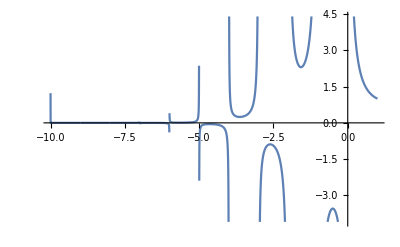

```mathematica
Plot[Gamma[x],{x,-10,1}]
```

```mathematica
Residue[Exp[1/z],{z,0}]
```

Residue[ⅇ^(1/z),{z,0}]

```mathematica
Residue[DiracDelta[x],{x,0}]
```

0

```mathematica
Table[Residue[1/z^n,{z,0}],{n,-5,5}]
```

{0,0,0,0,0,0,1,0,0,0,0}

```mathematica
Residue[Sin[x]/x,{x,0}]
```

0

```mathematica
Residue[1/((z-1)(z+1)^3),{z,-1}]
```

-1/8

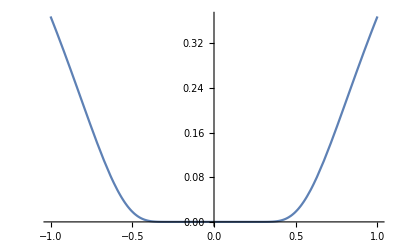

```mathematica
Plot[Exp[-1/z^2],{z,-1,1}]
```

```mathematica
BSSeries2[S_,K_,r_,σ_,T_]:=K*ⅇ^(-r*T)/2 *Sum[Sum[ (-1)^n/Gamma[1+(m-n)/2]*Z[σ,T]^(m+n)*Lo[S,K,r,T]^n
*Sum[Lo[S,K,r,T]^-j/Factorial[j],{j,0,n}],{m,1,20}],{n,0,20}]
```

```mathematica
BSSeries2[4000,4000,0.01,0.2,1]
```

315.025

```mathematica
BSSeries[4000,4000,0.01,0.2,1]
```

337.333

```mathematica
BSSeries3[S_,K_,r_,σ_,T_]:=K*ⅇ^(-r*T)/2 *Sum[Sum[ (-1)^n/(n! Gamma[1+(m-n)/2])*Z[σ,T]^(m-n)
*Sum[({{n}, {j}})Binomial[n,j]*Lo[S,K,r,T]^j Z[σ,T]^(-2*(n-j))/Factorial[j],{j,0,n}],{m,1,10}],{n,0,10}]
```

```mathematica
BSSeries3[4000,4000,0.01,0.2,1]
```

8.69537×10^21

```mathematica
BSSeries3[S_,K_,r_,σ_,T_]:=K*ⅇ^(-r*T)/2 *Sum[Sum[ (-1)^n/(n! Gamma[1+(m-n)/2])*Z[σ,T]^(m-n)
*Sum[Binomial[n,j]((-Lo[S,K,r,T])^j Z[σ,T]^(2*(n-j)))/(j!),{j,0,n}],{m,1,20}],{n,0,20}]
```

```mathematica
BSSeries3[4000,4000,0.01,0.2,1]
```

337.081

```mathematica
Subscript[C, m_,n_][S_,K_,r_,T_]:=((-1)^n(T/2)^((m+n)/2)Lo[S,K,r,T]^n)/Gamma[1+(m-n)/2]*Sum[Lo[S,K,r,T]^-j/Factorial[j],{j,0,n}];
Subscript[β, j_][S_,K_,r_,T_]:= K*Exp[-r*T]/2*Sum[Subscript[C, m,j-m][S,K,r,T],{m,1,j}];
BSseries4[S_,K_,r_,σ_,T_]:=Sum[Subscript[β, j][S,K,r,T]*σ^j,{j,1,20}]
```

```mathematica
BSSeries4[S_,K_,r_,σ_,T_]:=(K*Exp[-r*T])/2∑_(j=1)^20 ∑_(m=1)^j ((-Lo[S,K,r,T])^(j-m)*Z[σ,T]^j)/Gamma[1+m-j/2]*∑_(p=0)^(j-m) Lo[S,K,r,T]^-p/(p!)
```

```mathematica
BSSeries4[4000,4000,0.01,0.2,1]
```

315.025

```mathematica
Table[BSSeries[4000,4000,0.01,0.2,1]
```

```mathematica
BSSeries5[S_,K_,r_,σ_,T_]:=(K*Exp[-r*T])/2∑_(n=0)^20 ∑_(m=1)^20 (-1)^n/Gamma[1+(m-n)/2]*∑_(i=0)^n (Z[σ,T]^(m+n-2*i)(-Lo[S,K,r,T])^i)/((n-i)!)
BSSeries5[4000,4000,0.01,0.2,1]
```

337.842

```mathematica
BSSeries3[Lo_,Z_,K_,r_,T_,M_,N_]:=K*ⅇ^(-r*T)/2 *Sum[Sum[ (-1)^n/(n! Gamma[1+(m-n)/2])*(Z^2-Lo)^n*Z^(m-n),{m,1,M}],{n,0,N}];With[{Lo=1,K=4000,r=0.01,T=1},Expand[D[BSSeries3[Lo,Z,K,r,T,10,10],Z],Z]]
```

3917.81-0.0181828/Z^10+0.549525/Z^8-9.58753/Z^6+117.291/Z^4-949.866/Z^2-0.0109132 Z-950.765 Z^2-0.687535 Z^3+115.12 Z^4-11.3934 Z^5-38.3831 Z^6-43.0855 Z^7-26.4451 Z^8+26.1263 Z^9+41.6626 Z^10-26.1263 Z^11-27.4122 Z^12+43.0855 Z^13-27.9484 Z^14+11.3934 Z^15-3.24743 Z^16+0.687535 Z^17-0.111136 Z^18+0.0109132 Z^19

```mathematica
Table[With[{Lo=0.2,K=4000,r=0.01,T=1},BSSeries3[Lo,Z,K,r,T,M,M]],{Z,0.1,0.01,-0.01},{M,10,20,3}]//MatrixForm
```

(898.767 | 898.753 | 898.755 | 898.755
890.669 | 890.619 | 890.626 | 890.626
884.624 | 884.418 | 884.452 | 884.453
881.075 | 880.072 | 880.271 | 880.281
882.403 | 876.366 | 877.829 | 877.978
909.214 | 860.482 | 874.309 | 878.018
1212.01 | 605.246 | 762.729 | 943.505
7018.7 | -8113.63 | -11720.5 | 14125.8
312033. | -1.04609×10^6 | -7.86284×10^6 | 1.8942×10^7
1.9303×10^8 | -2.6505×10^9 | -3.34815×10^11 | 3.28798×10^12)